Induction and Recursion

## Introduction

In this chapter we describe how Mathematica can be used to help you make conjectures and prove them with mathematical induction and strong induction. We will also look at several examples of using Mathematica to explore recursive definitions and to implement recursive algorithms. Recursion is an important tool in any computer programming language, and Mathematica is no exception. We conclude with an example of proving program correctness of a Mathematica function.

## 5.1 Mathematical Induction

In this section we will demonstrate how to use Mathematica both to discover propositions and to aid in the use of mathematical induction to verify them. We begin with two examples of how to use Mathematica to discover and prove summation formulas. We then consider a question of divisibility.

### Summation Example 1

As our first example, we will explore a formula that you've already seen:

∑_(i=1)^n i=1+2+3+⋯+n=(n(n+1))/2

This formula is the subject of Example 1 in Section 5.1 of the text. Here, we will proceed as if we did not already know the formula.

#### Listing and Graphing to Find the Formula

Our first step is to discover the formula. To do this, we will have Mathematica compute the sums for a variety of values of n, using the Sum function.

The Sum function has essentially the same syntax as Table. The first argument is an expression representing the values to be added in terms of a variable. The second argument is a list indicating the values of the variable over which the sum should be computed. Refer to Section 2.4 for a  description of the behavior of the second argument. A table summarizing the main possibilities is shown below.

{i,i_max} | sum from i=1 to i_max
{i,i_min,i_max} | sum from i=i_min to i_max
{i,i_min,i_max,step} | sum from i=i_min to i_max by step
{i,list} | sum over i∈list

In our situation, we want to add the first several positive integers. For example, the sum of the first ten positive integers is

```mathematica
Sum[i,{i,10}]
```

55

To discover the formula for the sum of the first n positive integers, we need several specific examples to analyze. To calculate a lot of examples at once, we will embed the Sum function inside of a Table, with the maximum value of the summation as the table variable. This will produce the list of the sums of the first n positive integers for different values of n.

```mathematica
Table[Sum[i,{i,n}],{n,50}]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275}

Remember that we're working as if we do not already know the answer. Just looking at the data, you might notice a pattern, but if not, it's sometimes helpful to pair the value of n with the result. To do this, we only need to modify the Table function so that the first argument is the list whose first element is n and whose second is the Sum function.

```mathematica
Table[{n,Sum[i,{i,n}]},{n,50}]
```

{{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,28},{8,36},{9,45},{10,55},{11,66},{12,78},{13,91},{14,105},{15,120},{16,136},{17,153},{18,171},{19,190},{20,210},{21,231},{22,253},{23,276},{24,300},{25,325},{26,351},{27,378},{28,406},{29,435},{30,465},{31,496},{32,528},{33,561},{34,595},{35,630},{36,666},{37,703},{38,741},{39,780},{40,820},{41,861},{42,903},{43,946},{44,990},{45,1035},{46,1081},{47,1128},{48,1176},{49,1225},{50,1275}}

The entry {23,276} indicates that the sum of the first 23 positive integers is 276.

This still may not be enough to get an idea of what the formula could be, in which case a graph of the data can be of use. The ListPlot function is used to graph functions and data, and was first discussed in Section 2.3 of this manual. In this situation, we want to plot the points that the previous application of Table produced: {1,1},{2,3},{3,6},…. To do this, we apply ListPlot to the output above. Note that either of the previous two lists can be used. Given a list of pairs, ListPlot produces the graph interpreting the pairs as x-y coordinate pairs. Given a list of values, the values are interpreted as the y coordinates with the x coordinate being the position of the value in the list. That is, the first element is plotted at x-value 1, the second element at x-value 2, etc. In this case, the plots are identical, so we will use the shorter of the two expressions. Since Mathematica computes the sums quickly, we'll go out to a maximum of n = 1000. That way, we'll be sure to have a good idea of the shape of the graph.

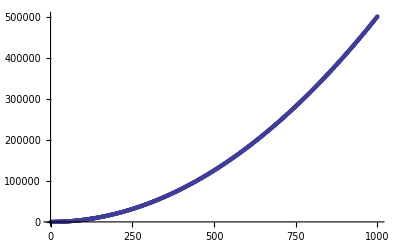

```mathematica
ListPlot[Table[Sum[i,{i,n}],{n,1000}]]
```

The particular values in the list may not have been helpful at all in figuring out what kind of formula we were looking for. But this graph probably looks very familiar. It looks very much like the right half of a parabola, suggesting that the formula is quadratic. (Of course, it may be cubic or quartic or some other polynomial, but we'll start with the simplest possibility based on the graph.)

#### Finding the Coefficients

Now that we have guessed the kind of formula, we can write it as f(n)=a·n^2+b·n+c. Determining the coefficients a, b, c is our next task. We will have Mathematica find them for us.

We already know a bunch of values for this function. Here are the first few again.

```mathematica
sumList=Table[Sum[i,{i,n}],{n,10}]
```

{1,3,6,10,15,21,28,36,45,55}

This data tells us a lot of information about our formula. For instance, if we plug in n=2, then f(2)=3, meaning

3=a·2^2+b·2+c=4a+2b+c

For n=1, we have

1=a+b+c

For n=3:

6=9a+3b+c

Mathematica can generate these equations for us. We can apply Table with first argument an equation, formed with the Equal (==) operator, representing the function f(n)=a·n^2+b·n+c. Instead of f(n), we use the data in sumList. So our expression will be sumList[[n]]==a*n^2+b*n+c.

```mathematica
sumEquations=Table[sumList[[n]]==a*n^2+b*n+c,{n,10}]
```

{1==a+b+c,3==4 a+2 b+c,6==9 a+3 b+c,10==16 a+4 b+c,15==25 a+5 b+c,21==36 a+6 b+c,28==49 a+7 b+c,36==64 a+8 b+c,45==81 a+9 b+c,55==100 a+10 b+c}

The list of equations stored as sumEquations is a system of equations. In particular, we have 10 equations in three variables. You have probably seen systems of at least 2 and 3 equations in 2 or 3 variables in previous mathematics courses. You can have Mathematica solve the system of equations by applying the Solve function to the list. We provide Solve with the list of equations and the list of variables appearing in them. (The second argument can often be omitted and Mathematica will deduce the variables.)

```mathematica
Solve[sumEquations,{a,b,c}]
```

{{a→1/2,b→1/2,c→0}}

You may recall that to solve a system of equations in three unknowns, only three equations are required. In this situation, having more equations is useful. If we were wrong about the formula being quadratic but attempted to find coefficients with only three equations, Mathematica may still have found values for a, b, and c that satisfied the three equations we chose. With ten equations, if the actual formula were not quadratic, there is a greater chance that no values of a, b, and c would satisfy all ten equations. In that case, Mathematica would have returned an empty list to indicate the absence of a solution and that our guess about the kind of formula was incorrect.

Let's review what we've done so far. Our goal is to find a formula for the sum ∑_(i=1)^n i. We used Mathematica to compute a bunch of values of this sum and graphed them. This graph suggested a quadratic formula, i.e., one of the form a·n^2+b·n+c for some values of a, b, and c. We then used Mathematica's Solve function to determine that a=b=1/2 and c=0. In other words, we've found the formula 1/2 n^2+1/2 n, which, of course, is the same as (n(n+1))/2. Although we have found a formula, we have not yet proven anything, we've only made a conjecture.

#### The Induction Proof

To prove that our formula is correct, we use mathematical induction. First, let's make our formula into a function.

```mathematica
sumF[n_]:=(1/2)*n^2+(1/2)*n
```

To complete the basis step of the induction, we need to see that the formula agrees with the sum for n=1.

```mathematica
Sum[i,{i,1}]
```

1

```mathematica
sumF[1]
```

1

They are equal and the basis step is verified.

For the inductive step, we assume that the formula is correct for k and need to demonstrate that it is true for k+1. In Example 1 in the textbook, this was done by starting with the sum 1+2+⋯+k+(k+1) and applying the inductive hypothesis to the first k terms to obtain (k(k+1))/2+(k+1). Then algebra is used to turn that expression into the formula evaluated at k+1. With Mathematica, we can just check whether the expressions are the same.

The sum of the first k+1 terms is 1+2+⋯+k+(k+1)=f(k)+(k+1).

```mathematica
sumF[k]+(k+1)
```

1+(3 k)/2+k^2/2

That used the inductive hypothesis. We need to see if this is the same as f(k+1).

```mathematica
sumF[k+1]
```

(1+k)/2+1/2 (1+k)^2

To check whether f(k+1) is the same as f(k)+(k+1), we will apply the Reduce function. The first argument to Reduce will be the equation formed by identifying the two expressions. The second argument is the variable k. Reduce will apply algebraic rules to the expression to determine the values of k for which the equation holds. If there is more than one equation or more than one variable, you can use a list in either argument.

```mathematica
Reduce[sumF[k]+(k+1)==sumF[k+1],k]
```

True

The output True indicates that the equation is valid for all values of k, in particular, it is true for the positive integers. This means that the inductive step is verified, and hence the formula is correct.

### Summation Example 2

As a second example of using Mathematica to find and prove summation formulae, consider the sum ∑_(i=1)^n i^2(i+1)!. For this example, we won't go through the process of computing values and graphing as we did above. That is a very valuable process, and we strongly recommend that you go through it yourself with a few examples. But Mathematica includes a function that will give us the result.

#### Using Sum to Determine the Formula

Above, we used the Sum function to determine the numeric sum of a sequence of numbers. While the numbers being added were determined by a formula, nevertheless the bounds of the sum were explicit so that specific values could be calculated and added. To calculate ∑_(i=1)^10 i^2(i+1)!, we use Sum as in the previous example, with the formula given as the first argument. The bounds, i ranging from 1 to 10, are given in the second argument in the form {i,10}.

```mathematica
Sum[i^2*(i+1)!,{i,10}]
```

4311014402

(Note the use of the exclamation mark for the computation of factorial. You can also use the functional form Factorial if you prefer.)

The Sum function can also be used for computing symbolic sums, as in ∑_(i=1)^n i^2(i+1)!. All we need to do is replace the upper bound of 10 with the symbol n, provided that n has not been assigned a value.

```mathematica
Sum[i^2*(i+1)!,{i,n}]
```

2-(2+n)!+n (2+n)!

Applying Simplify to the output, we obtain a slightly simpler formula.

```mathematica
Simplify[%]
```

2+(-1+n) (2+n)!

Note that you can use symbols in place of any of the bound specifications. You can also use the symbol Infinity in place of the upper bound, provided the series is convergent.

Similarly, Mathematica provides the Product function for computing numeric and symbolic products. The syntax is the same.

#### The Induction Proof

Now that the Sum function has determined the formula ∑_(i=1)^n i^2(i+1)! =(n-1)(n+2)!+2, we will use Mathematica to help us prove it. Even though we can be very confident that Mathematica has given us a correct formula, applying a Mathematica function is not the same as a proof.

As before, we'll define a function based on the formula.

```mathematica
sumF2[n_]:=(n-1)*(n+2)!+2
```

For the basis step of the induction, we need to see that the formula holds for n=1. The value of the sum for n=1 is

```mathematica
1^2*(1+1)
```

2

And the formula applied to n=1 is

```mathematica
sumF2[1]
```

2

The basis step is verified.

For the inductive step, we assume that the formula is correct for k. That is, we assume that

∑_(i=1)^k i^2(i+1)! =(k-1)(k+2)!+2

We need to show that the formula works for k+1. Now,

∑_(i=1)^(k+1) i^2(i+1)! =∑_(i=1)^k i^2(i+1)!+(k+1)^2((k+1)+1)!

Using the inductive hypothesis that the formula is correct for k, this is

```mathematica
sumF2[k]+(k+1)^2*((k+1)+1)!
```

2+(-1+k) (2+k)!+(1+k)^2 (2+k)!

We need to check to see if this is the same as the formula applied to k+1.

```mathematica
sumF2[k+1]
```

2+k (3+k)!

Again, we use Reduce applied to the equation formed by identifying these two expressions.

```mathematica
Reduce[sumF2[k]+(k+1)^2*((k+1)+1)!==sumF2[k+1]]
```

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

True

Observe that a warning message was produced this time. The reason for this is the inclusion of the factorials, which Mathematica treats with particular care. However, the output is correct, the equation is true, as you can verify by hand.

It should be pointed out that this “proof” of the formula for the sum is only correct modulo the correctness of the Mathematica functions that we have used and the proper functioning of the computer it is run on. One of the drawbacks of computer-aided proof is the degree to which your computer or software could be introducing hidden errors.

### Divisibility

For a final example, we'll see how Mathematica can be used to help prove results about divisibility. In Example 8 from Section 5.1 of the text, it was shown that n^3-n is divisible by 3 for all positive integers n. Exercise 33 asks you to prove that n^5-n is divisible by 5 for all positive integers. These two facts suggest that perhaps n^7-n is divisible by 7 for all positive integers n. Let's see how Mathematica can help us prove this fact.

We begin by creating a function to represent the expression n^7-n.

```mathematica
divisibleEx[n_]:=n^7-n
```

The basis case is n=1. For n=1, the expression is

```mathematica
divisibleEx[1]
```

0

This is divisible by 7, so the basis case holds.

The inductive hypothesis is that k^7-k is divisible by 7 for a positive integer k. We need to show that (k+1)^7-(k+1) is divisible by 7. To do this, we'll use the following fact: if n|a and n|b-a then n|b. (The reader should verify this statement, which is equivalent to Theorem 1, part (i), of Section 4.1.)

By assumption, 7 divides k^7-k. We will have Mathematica compute the difference with (k+1)^7-(k+1).

```mathematica
divisibleEx[k+1]-divisibleEx[k]
```

-1-k^7+(1+k)^7

We apply the Expand function to the result.

```mathematica
Expand[%]
```

7 k+21 k^2+35 k^3+35 k^4+21 k^5+7 k^6

You can see that the coefficients are all multiples of 7 and thus the expression is divisible by 7. We can confirm this with Mathematica by checking that the difference is divisible by 7 by using the Reduce function on the equation formed by setting the difference equal to 0 and invoking the Modulus option.

```mathematica
Reduce[divisibleEx[k+1]-divisibleEx[k]==0,Modulus->7]
```

True

Thus, the inductive step is verified and hence n^7-n is divisible by 7 for all positive integers n.

## 5.2 Strong Induction and Well-Ordering

In this section, we'll see one way that Mathematica can be used to support a proof by strong induction. In particular, we will consider the class of problems illustrated in Example 4: prove that every amount of postage of 12 cents or more can be formed using just 4-cent and 5-cent stamps. The second solution to that example will form the model for this discussion. (See also Exercises 3 through 8 as other examples of problems of this kind.)

The basis step of the induction argument requires several propositions to be verified. Using the notation in the text, the propositions P(b),P(b+1),…,P(b+j) must all be demonstrated for some integer b and a positive integer j. Mathematica can be useful in these situations because it can often verify the basis cases for you. This is particularly useful when j is large.

Showing that every amount of postage over 12 cents can be formed using 4 and 5 cent stamps requires 4 basis cases: P(12),P(13),P(14),P(15). We begin by showing how to use Mathematica to demonstrate P(12), that postage of 12 cents can be formed using 4 and 5 cent stamps. While you may object that it is obvious that 12=4·3, our ultimate goal is to generalize our code to encompass the entire class of postage problems.

#### Making Postage

To verify P(12), we must find nonnegative integers a and b, representing the number of stamps of the two denominations, such that 12=4a+5b. The most straightforward way of finding a and b is to test all the possibilities. We know that a and b must both be nonnegative.

Also, the maximum possible values of a and b are ⌊12/4⌋ and ⌊12/5⌋, respectively. (Recall that ⌊x⌋ is the notation used to represent the floor of x, that is, the largest integer less than or equal to x.) To see why this is so, consider b: 12=4a+5b≥5b since a≥0. That is, 5b≤12 and so b≤12/5. And since b must be an integer, we have b≤⌊12/5⌋. Likewise for a.

Since a and b must be between 0 and the floor of 12 divided by 4 or 5, respectively, we can use a pair of nested For loops to check all the possible values. Within the loops, we only need to check to see if 4a+5b=12. If so, we'll terminate the loops, which we enclose in a Catch, by applying Throw to the pair {a,b}.

```mathematica
Catch[
For[a=0,a≤Floor[12/4],a++,
For[b=0,b≤Floor[12/5],b++,
If[4*a+5*b==12,Throw[{a,b}]]
]
]
]
```

{3,0}

We can very easily generalize this by replacing the target value and the stamp denominations with variables. The following function implements this generalization. It accepts the two denominations and the target value as input and returns a list whose elements represent the number of each kind of stamp required. In the event that the function fails to form the desired amount of postage with the given stamps, it returns Null.

```mathematica
makePostage[stampA_Integer,stampB_Integer,postage_Integer]:=Module[{a,b},
Catch[
For[a=0,a≤Floor[postage/stampA],a++,
For[b=0,b≤Floor[postage/stampB],b++,
If[stampA*a+stampB*b==postage,Throw[{a,b}]]
]
]
]
]
```

Applying makePostage with stamps 4 and 5 and postage 13 tells us that it requires two 4-cent stamps and one 5 cent stamps to make 13 cents postage.

```mathematica
makePostage[4,5,13]
```

{2,1}

On the other hand, it is not possible to make 11 cents postage with 4 and 5 cent stamps and so the function does not produce output.

```mathematica
makePostage[4,5,11]
```

#### Automating the Basis Step

The makePostage function finds the number of stamps of each denomination needed to produce the desired postage. As such, it verifies individual basis step propositions. With a simple loop, we can verify all of the basis cases. Recall that the basis step was to verify that postage can be made for 12, 13, 14, and 15 cents.

```mathematica
For[p=12,p≤15,p++,
Print[makePostage[4,5,p]]
]
```

{3,0}

{2,1}

{1,2}

{0,3}

We will make a function for this in a moment, but first observe that the number of propositions in the basis step is equal to the smaller denomination stamp. The reason for this is in the proof of the inductive step. You should review the second solution to Example 4 in the text. The key point is that to make postage of k+1 cents, the proof relies on the inductive assumption that you can make postage of k+1-4=k-3 cents. This requires that k-3≥12, or k≥15.

Generically, if a is the smaller of the stamps and x is the minimum postage that we claim can be made (x=12 in the example), then the inductive step requires k+1-a≥x. Which is to say k≥x+(a-1). Thus P(x),P(x+1),…,P(x+(a-1)) must form the basis step.

This is useful to us in the following way: given the values of the stamps and the minimum value of postage, we can automate the verification of the appropriate basis cases.

We first create the following message to be given in case one of the basis cases fails. Note the use of placeholders `1`, `2`, and `3`. These serve as variables. When Message is called, it will be given with three additional arguments, beyond the name of the message, and the values of these arguments will be substituted in for these variables.

```mathematica
postageBasis::fail="Cannot form postage of `3` using stamps of amounts `1` and `2`.";
```

Here is the postageBasis function. Note that the expression postageList terminates the first argument of Check, and Null is the second argument of Check. Consequently, if the main body of the function, contained in the first argument of Check, is successful, the result of the function will be the list of rules that specify the numbers of stamps needed for each amount of postage. If there is an amount of postage that is not possible, then the message will be generated and the result of the function will be Null.

```mathematica
postageBasis[stampA_Integer,stampB_Integer,minpostage_Integer]:=Module[{small,postageList={},postage,R},
small=Min[stampA,stampB];
Check[
For[postage=minpostage,
postage≤minpostage+small-1,
postage++,
R=makePostage[stampA,stampB,postage];
If[R=!=Null,
AppendTo[postageList,postage->R],
Message[postageBasis::fail,stampA,stampB,postage]
]
];
postageList,(*end of Check argument 1*)
Null
]
]
```

We apply it to the example of using 4 and 5 cent stamps to make postage of at least 12 cents.

```mathematica
postageBasis[4,5,12]
```

{12→{3,0},13→{2,1},14→{1,2},15→{0,3}}

The postageBasis function above accepts as input the denominations of the two stamps, and the minimum value such that all postage values equal to or greater than that minimum can be made. The function uses the Min command to set small equal to the lesser of the two denominations. The postageList variable is used to store the information that shows how to make the various amounts of postage. This list will store rules of the form postage→{a,b} which indicate that the specified amount of postage can be made with a stamps of value A and b of B.

The For loop considers each of the basis cases (using the observation above). For each amount of postage, we use makePostage to determine if it is possible to form that postage from the stamp values. If so, makePostage returns a pair indicating how the desired postage is made and this is added to the postageList.

Check evaluates its first argument and the output of the Check is the output of the first argument, unless a message had been raised, in which case the second argument is evaluated. If makePostage ever returns Null, that indicates that the particular basis case cannot be verified. In this case, the message postageBasis::fail is raised. If no messages are raised, that means that every amount of postage succeeded and postageList, the last expression of the first argument to Check is output.

The following indicates that it is false that every amount of postage of 12 cents or larger can be obtained using 4 and 6 cent stamps.

```mathematica
postageBasis[4,6,12]
```

postageBasis::fail: Cannot form postage of 13 using stamps of amounts 4 and 6.

postageBasis::fail: Cannot form postage of 15 using stamps of amounts 4 and 6.

## 5.3 Recursive Definitions and Structural Induction

In this section we will show how functions and sets can be defined recursively in Mathematica.

### A Simple Recursive Function

First we consider the recursively defined function from Example 1 in Section 5.3 of the text. This function is defined by f(0)=3 and f(n+1)=2·f(n)+3.

In order to represent this function in Mathematica, we must transform the recursive part of the definition into an equation for f(n) instead of f(n+1). We have to decrease all of the arguments in the recursive part of the definition by 1: f(n)=2·f(n-1)+3. The formula f(n+1)=2·f(n)+3 is perhaps more expressive in that the n+1 suggests that the definition is about the “next” value of the function. But Mathematica cannot interpret n+1 as a parameter in a function definition, at least not in a natural way.

It is also important to point out that changing the recursive formula also changes the domain over which it is valid. The formula f(n+1)=2·f(n)+3 applies for all n≥0, while f(n)=2·f(n-1)+3 applies for all n≥1. This does not affect the value of f(n) for any n.

The most natural way to define a recursive function is to define the function just like any other. In this case, the function will refer to itself, but Mathematica has no problem with that.

```mathematica
f[n_]:=2*f[n-1]+3
```

We also must define the basis step. To declare f(0)=3, you make the assignment as shown below.

```mathematica
f[0]=3
```

3

Note that the recursive part of the definition must be given as a SetDelayed (:=). The basis step can be defined with either Set (=) or SetDelayed (:=).

Now that the recursive definition and the basis step have been assigned, you can use f like any other function.

```mathematica
f[10]
```

6141

And you can compute the values of f from 1 to 9 using Table.

```mathematica
Table[f[n],{n,9}]
```

{9,21,45,93,189,381,765,1533,3069}

#### Down Values

It is worth understanding a bit of what Mathematica is doing when you define and evaluate a recursively defined function. Any time you evaluate a function, Mathematica checks the function’s list of down values. We first discussed down values in Section 2.3. Briefly, the down values for a symbol are the expressions associated with the symbol when it is given arguments, as opposed to the symbol by itself.  Here are the down values for the function f.

```mathematica
DownValues[f]
```

{HoldPattern[f[0]]:>3,HoldPattern[f[n_]]:>2 f[n-1]+3}

This indicates that f has two down values: one associated to the argument 0 and one to arguments matching the pattern n_.

Whenever you apply Set (=) or SetDelayed (:=) with the left hand side of the operator of the form f[…], Mathematica understands this to be the creation or modification of one of f’s down values. Note that such an assignment does not affect any down values other than the one, if any, whose left hand side is of exactly the same form. Consequently, when dealing with recursive functions, it is a good idea to apply Clear to a function name when redefining a function, as this will remove all the down values for the symbol.

When you evaluate f at a particular value, Mathematica checks the more specific down values first. That is, if you enter f[0], Mathematica will use the down value associated to f[0] and output 3 rather than applying the formula 2*f[0-1]+3.

If you apply f to 0, Mathematica sees that 0 has a specific down value and returns the value. If you apply f to a different value, say 2, Mathematica does not find a specific down value for 2 and so it applies the formula. The formula says that f(2)=2·f(1)+3. When Mathematica tries to evaluate this, it recognizes that it needs to find f(1). Again, it checks the down values and, not finding a result for 1, it applies the formula f(1)=2·f(0)+3. Since f(0) has a specific value, Mathematica looks up f(0), which allows it to compute f(1)=9 and then f(2)=21.

You may be wondering why the output above indicates that f's list of down values only has the value for f(0), even though we've computed other values. The reason is that Mathematica doesn't automatically store down values. Most of the time, you don't execute functions on the same input multiple times, so it would be a waste of memory to store every value computed. You have to explicitly tell Mathematica to store down values.

We have seen that you can store a specific value as a down value by making an assignment such as f[0]=3. An assignment of this form can be given within the body of a function. Doing so causes the function to store values as it calculates them, as we’ll see below.

### A Second Recursive Function

Now consider the function F defined by the basis values F(0)=1 and F(1)=1 and the recursive formula F(n)=F(n-1)+F(n-2). This is the function whose values are the Fibonacci numbers.

We will define this function as indicated above. First, we establish the basis values.

```mathematica
F[0]=1;
F[1]=1;
```

Note that these have been stored as down values.

```mathematica
DownValues[F]
```

{HoldPattern[F[0]]:>1,HoldPattern[F[1]]:>1}

For the recursive part of the definition, we enter the following.

```mathematica
F[n_]:=F[n]=F[n-1]+F[n-2]
```

This may look a bit strange, but it is actually fairly straightforward. The expression is an application of SetDelayed (:=), which is an assignment to the symbol F with argument matching the pattern n_, i.e., with any argument. Note that this has created a single entry in the down values list.

```mathematica
DownValues[F]
```

{HoldPattern[F[0]]:>1,HoldPattern[F[1]]:>1,HoldPattern[F[n_]]:>(F[n]=F[n-1]+F[n-2])}

The “value” associated to F with argument matching n_ is the expression F[n]=F[n-1]+F[n-2]. It can be useful to think of F as representing both a function and a computer program. Assigning F[0]=1 and F[1]=1 establish the basis values for the function F. Setting F[n_] defines the action of the program F. That program has a single line of code which is F[n]=F[n-1]+F[n-2]. That line of code in the program sets a particular value of the function F.

The function F is now completely defined and produces correct output.

```mathematica
Table[F[n],{n,0,10}]
```

{1,1,2,3,5,8,13,21,34,55,89}

Also note that, unlike the function f above, F has added the results of its calculations to its down values.

```mathematica
DownValues[F]
```

{HoldPattern[F[0]]:>1,HoldPattern[F[1]]:>1,HoldPattern[F[2]]:>2,HoldPattern[F[3]]:>3,HoldPattern[F[4]]:>5,HoldPattern[F[5]]:>8,HoldPattern[F[6]]:>13,HoldPattern[F[7]]:>21,HoldPattern[F[8]]:>34,HoldPattern[F[9]]:>55,HoldPattern[F[10]]:>89,HoldPattern[F[n_]]:>(F[n]=F[n-1]+F[n-2])}

### Comparing Complexity

The difference in time complexity between a recursive function that stores computed values and one that does not is very significant, perhaps much more than you might think. Let's create two new functions, both of which model the function g(n)=2·g(n-1)+3·g(n-2) with g(0)=5 and g(1)=2. The function gR will “remember” computed values while gF will be “forgetful” and not store values.

We will track the recursive calls by adding a Print statement every time the formula is used. Here are the two functions.

```mathematica
gR[n_]:=Module[{},
Print["Computing gR[",n,"]"];
gR[n]=2*gR[n-1]+3*gR[n-2]
]
gR[0]=5;
gR[1]=2;
```

```mathematica
gF[n_]:=Module[{},
Print["Computing gF[",n,"]"];
2*gF[n-1]+3*gF[n-2]
]
gF[0]=5;
gF[1]=2;
```

Let’s see what happens when we attempt to compute gR[5].

```mathematica
gR[5]
```

Computing gR[5]

Computing gR[4]

Computing gR[3]

Computing gR[2]

422

This appears fairly straightforward. We enter gR[5], and since this has not been stored as a down value, the formula is evaluated, causing the print statement to be executed. Then, since g(5) depends on g(4) and g(3), Mathematica needs to know, first, the value of g(4). Since this has not been previously computed, again the formula needs to be invoked causing Mathematica to print “Computing gR[4]”. Computing g(4) requires the values for g(3) and g(2). Again, g(3) is needed first, so Mathematica executes gR[3]. This requires g(2) and g(1). To obtain the value for g(2), the formula must be invoked once again.

After printing “Computing gR[2]”, Mathematica needs to evaluate the expression gR[2]=2*gR[1]+3*gR[0]. This time, it can look to the stored values of gR[1] and gR[0] to compute that g(2)=19. This value is stored as a down value of gR, and we begin unwinding. gR[2] was called when attempting to compute gR[3], which depends on values for 2 and 1. Since gR[2] was just returned and gR[1] is stored, gR[3] can be computed and stored. The value of gR[3] is sent back up to the computation of gR[4]. gR[4] depends on values of 3 and 2 and both of those values are now available, so gR[4] can be computed. Likewise, gR[5] can be determined using the values of gR[4] and gR[3].

Contrast this with what happens for gF[5].

```mathematica
gF[5]
```

Computing gF[5]

Computing gF[4]

Computing gF[3]

Computing gF[2]

Computing gF[2]

Computing gF[3]

Computing gF[2]

422

Things begin the same. We execute gF[5] causing the print statement to report the fact that we are computing that value. To obtain gF[5], we need the values of gF[4] and gF[3]. gF[4] is computed first, since it is leftmost in the formula and “Computing gF[4]” is displayed. To obtain the value for 4, we need the values for 3 and 2, and so gF[3] is executed. This requires the values for gF[2] and gF[1]. Again, since it is leftmost, gF[2] is tackled first, causing “Computing gF[2]” to be displayed.

This value can be computed from the stored values gF[1] and gF[0]. That means that gF[2], which was invoked in the attempt to compute gF[3], is complete and we move back up to the computation of gF[3]. Since gF[3] depends on the recently computed gF[2] and on gF[1], which was stored as an initial condition, gF[3] can be computed as well.

This means that gF[4] now knows the value of gF[3]. You can think about it as if the formula gF[4] is working with is now 2*44+3*gF[2]. gF[4] now just needs the value of gF[2]. gR could just look that value up, since it had recorded the value gR[2] when it was first computed. But gF is not storing values that are computed, so it must apply the formula to compute gF[2] again. Thus, “Computing gF[2]” is displayed a second time. Once the formula has been used to once again compute gF[2], then this value is available to gF[4] to complete its computation.

Once gF[4] has finished computing, that value is sent up. gF[5], which required gF[4] and gF[3], now knows one of the two values it required. But again, gF[3], which was computed as part of gF[4], must be computed all over again. Consequently, you see the message “Computing gF[3]” again. And gF[3] requires the value for 2, so gF[2] must be executed a third time.

As you can imagine, the difference between storing values and not is even more extreme for larger input values. When values are stored, once the recursion starts working its way back up the ladder, it remembers all the results from the lower values. When values are not stored, the chain of recursive calls has to keep recomputing the results from lower valued inputs.

### A Recursive Function with Two Parameters

In Example 13 of Section 5.3 of the text, the sequence a_(m,n) is defined. We will define a function A(m,n) that models the sequence a_(m,n). The basis value is A(0,0)=0, and the recursion formula is

A(m,n)=Piecewise[{{A(m-1,n)+1, if n=0 and m>0}, {A(m,n-1)+n, if n>0}}]

As with the previous example, we will define the function so as to store values. The initial value is as follows.

```mathematica
A[0,0]=0;
```

We will define the recursive formula using a Which. Recall that the Which function accepts an even number of arguments, with the first in each pair a condition and the second in the pair evaluated if the condition holds.

```mathematica
A[m_,n_]:=A[m,n]=Which[n==0&&m>0,A[m-1,n]+1,n>0,A[m,n-1]+n]
```

Now we can compute some values of a_(m,n).

```mathematica
A[3,2]
```

6

```mathematica
A[5,3]
```

11

To get a better idea of what the values of a_(m,n) are, we can display a Table of them using TableForm.

```mathematica
Table[A[m,n],{m,0,10},{n,0,10}]//TableForm
```

0 | 1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55
1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57
3 | 4 | 6 | 9 | 13 | 18 | 24 | 31 | 39 | 48 | 58
4 | 5 | 7 | 10 | 14 | 19 | 25 | 32 | 40 | 49 | 59
5 | 6 | 8 | 11 | 15 | 20 | 26 | 33 | 41 | 50 | 60
6 | 7 | 9 | 12 | 16 | 21 | 27 | 34 | 42 | 51 | 61
7 | 8 | 10 | 13 | 17 | 22 | 28 | 35 | 43 | 52 | 62
8 | 9 | 11 | 14 | 18 | 23 | 29 | 36 | 44 | 53 | 63
9 | 10 | 12 | 15 | 19 | 24 | 30 | 37 | 45 | 54 | 64
10 | 11 | 13 | 16 | 20 | 25 | 31 | 38 | 46 | 55 | 65

Note that the first variable to be specified is shown in rows. That is, the first row corresponds to m=0, the second row has m=1, etc.

### A Recursively Defined Set

In Example 5, the text describes how to recursively define a set. Here, we will consider a slightly more complicated example.

Let S be the subset of the integers defined by:

Basis step: 4∈S and 7∈S.

Recursive step: if x∈S and y∈S, then x+y∈S.

(Note that this is the set of all postage that can be formed with 4 cent and 7 cent stamps.)

To model S in Mathematica, we will define a list that includes the elements called for in the basis step. For the recursive step, we will define a function that applies the recursion to the set.

The basis step requires that 4 and 7 are members of S. So we define S to be the list consisting of 4 and 7.

```mathematica
S={4,7}
```

{4,7}

To implement the recursive step, we will create a function recurseS. This function will accept as input the current S and will return the list obtained after applying the recursive rule. For instance, in the first application of recurseS, the procedure needs to add 4+4, 4+7, 7+4, and 7+7. (We will eliminate duplication by applying the Union function.)

We will use a Do loop. Recall that in a Do loop, the first argument is the expression that is evaluated. Subsequent arguments specify the loop variables. Also recall that a variable specification of the form {i,list} causes i to take on each element of the list.

Here is the function.

```mathematica
recurseS[S_List]:=Module[{x,y,T=S},
Do[T=Union[T,{x+y}],{x,S},{y,S}];
T
]
```

Now we apply this function to S.

```mathematica
S=recurseS[S]
```

{4,7,8,11,14}

After a second iteration:

```mathematica
S=recurseS[S]
```

{4,7,8,11,12,14,15,16,18,19,21,22,25,28}

A third:

```mathematica
S=recurseS[S]
```

{4,7,8,11,12,14,15,16,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,46,47,49,50,53,56}

### A Set of Strings

As the final example in this section, we will look at how to generate sets of strings over a finite alphabet, as described in Definition 1 of Section 5.3.

The alphabet we will use is {"a","b","c","d"}. We begin by assigning this to a name.

```mathematica
alphabet={"a","b","c","d"}
```

{a,b,c,d}

According to Definition 1, the basis step is that our set of strings must contain the empty string. In Mathematica, the empty string is given by "". We will use the name S2 for our set of strings, since S is used above.

```mathematica
S2={""}
```

{}

Note that while the output makes this appear to be an empty list, applying FullForm reveals that it does in fact contain the empty string.

```mathematica
S2//FullForm
```

List[""]

Like the previous example, we will create a function to build the set of strings. The recursive step in the definition tells us that we build the set by combining every element of S2 with every letter in the alphabet. Again we will use a Do loop with two loop variables. We will define the function to accept the current version of the set and the alphabet as arguments.

To combine two strings, we apply the StringJoin (<>) operator. Here is the function.

```mathematica
buildStrings[S_List,A_List]:=Module[{T=S,w,x},
Do[T=Union[T,{w<>x}],{w,S},{x,A}];
T
]
```

The first application of the recursion adds the alphabet to the set.

```mathematica
S2=buildStrings[S2,alphabet]
```

{,a,b,c,d}

Again, since Mathematica does not display the enclosing quotation marks of strings in its output, the initial comma in the output above is separating the empty string from “a”. The second application adds all the two-character strings.

```mathematica
S2=buildStrings[S2,alphabet]
```

{,a,aa,ab,ac,ad,b,ba,bb,bc,bd,c,ca,cb,cc,cd,d,da,db,dc,dd}

The third application includes the three-character strings.

```mathematica
S2=buildStrings[S2,alphabet]
```

{,a,aa,aaa,aab,aac,aad,ab,aba,abb,abc,abd,ac,aca,acb,acc,acd,ad,ada,adb,adc,add,b,ba,baa,bab,bac,bad,bb,bba,bbb,bbc,bbd,bc,bca,bcb,bcc,bcd,bd,bda,bdb,bdc,bdd,c,ca,caa,cab,cac,cad,cb,cba,cbb,cbc,cbd,cc,cca,ccb,ccc,ccd,cd,cda,cdb,cdc,cdd,d,da,daa,dab,dac,dad,db,dba,dbb,dbc,dbd,dc,dca,dcb,dcc,dcd,dd,dda,ddb,ddc,ddd}

#### A General Function

We can put this process all together in one function. Given a set of strings representing the alphabet and a positive integer indicating the number of iterations desired, the following function will return the set of strings obtained after the given number of iterations.

```mathematica
allStrings[A_List,n_Integer]:=Module[{S={""},i},
For[i=1,i≤n,i++,
S=buildStrings[S,A]
];
S
]
```

Below, we apply this function to the alphabet consisting of the strings “ab” and “ba” (in discrete mathematics, an alphabet does not have to consist of individual letters).

```mathematica
allStrings[{"ab","ba"},4]
```

{,ab,abab,ababab,abababab,abababba,ababba,ababbaab,ababbaba,abba,abbaab,abbaabab,abbaabba,abbaba,abbabaab,abbababa,ba,baab,baabab,baababab,baababba,baabba,baabbaab,baabbaba,baba,babaab,babaabab,babaabba,bababa,bababaab,babababa}

## 5.4 Recursive Algorithms

In this section we will use Mathematica to implement several different recursive algorithms. First, we will look at two different recursive implementations of modular exponentiation and compare their performance. Then we will contrast a recursive approach to computing factorial with an iterative approach. And finally, we will provide an implementation of merge sort.

### Modular Exponentiation

Example 4 of Section 5.4 of the text describes two recursive approaches to computing b^n mod m. Both of these use the initial condition b^0 mod m=1. The first approach is based on the fact that b^n mod m=(b·(b^(n-1)mod m))mod m.

The second approach is based on the observation that for even exponents, we can compute via the formula b^n mod m=(b^(n/2)mod m)^2 mod m. And if the exponent is odd, we can use the identity b^n mod m=((b^⌊n/2⌋mod m)^2 mod m)·(b mod m) mod m.

#### Approach 1

First we will implement exponentiation based on the initial condition b^0 mod m=1 and the formula b^n mod m=(b·(b^(n-1)mod m))mod m. The function power1 will accept three arguments: the base b, the exponent n, and the modulus m.

If the exponent is 0, then regardless of the base or the modulus, the function returns 1. We can specify that behavior as follows. Observe that it is not necessary to give names to the other two arguments, since their specific values are irrelevant.

```mathematica
power1[_Integer,0,_Integer]:=1
```

In Mathematica, you are allowed to provide multiple definitions for the same function, provided the arguments have different forms. If two definitions both match a particular set of arguments, then the definition that is issued first, and is thus first in the list of down values, is the one applied. However, it is generally a good idea to ensure that the two patterns do not overlap. Consequently, for the recursive part of power1, we will explicitly insist that the exponent be positive.

If the exponent is greater than 0, then we compute the product of the base with the function applied to the same base and modulus but the power decreased by 1. To ensure that the exponent is in fact positive, we will impose a Condition (/;) by entering the operator /; following by the proposition n>0 between the argument list and the SetDelayed (:=) operator.

```mathematica
power1[b_Integer,n_Integer,m_Integer]/;n>0:=Mod[b*power1[b,n-1,m],m]
```

Notice that the down values of the symbol power1 now includes both definitions.

```mathematica
DownValues[power1]
```

{HoldPattern[power1[_Integer,0,_Integer]]:>1,HoldPattern[power1[b_Integer,n_Integer,m_Integer]/;n>0]:>Mod[b power1[b,n-1,m],m]}

Note that we did not store computed values in this function. The reason for this is that each iteration of the function only depends on one other call to the function. This is in contrast with the gR and gF functions from the previous section. Those functions called themselves twice in each iteration. As a result, those functions made use of the same value multiple times. When deciding whether or not to store values, you must weigh its potential benefit for not unnecessarily repeating computations with the cost of storage requirements.

We can use power1 to compute 3^6 mod 7 and compare the result to Mathematica’s computation of the same expression.

```mathematica
power1[3,6,7]
```

1

```mathematica
Mod[3^6,7]
```

1

#### Approach 2

The second approach computes the power based on Algorithm 4 from Section 5.4. For exponent 0, it returns 1, just as before. If the exponent is even, then the algorithm uses the formula b^n mod m=(b^(n/2)mod m)^2 mod m, and for odd powers, it computes the power using the identity b^n mod m=((b^⌊n/2⌋mod m)^2 mod m)·(b mod m) mod m.

Since there are three possibilities, 0, even, or odd, we give the definition in three parts.

```mathematica
power2[_Integer,0,_Integer]:=1;
power2[b_Integer,n_Integer,m_Integer]/;n>0&&EvenQ[n]:=Mod[power2[b,n/2,m]^2,m];
power2[b_Integer,n_Integer,m_Integer]/;n>0&&OddQ[n]:=Mod[Mod[power2[b,Floor[n/2],m]^2,m]*b,m];
```

We apply power2 to 3^6 mod 7 as well.

```mathematica
power2[3,6,7]
```

1

#### Comparing Performance of the Functions

Now that we've implemented these two algorithms, let's compare their performance on a variety of input values.

We fix the base 3 and the modulus 7 and consider the exponents from 100 to 1000. To compare the performance, we'll time the execution of each function on the exponents from 100 to 1000. We use Table to build the two lists consisting of the exponent/time pairs. Recall that Timing returns a list consisting of the time taken and the result, so we apply the Part ([[…]]) operator to extract the time.

In order to obtain results with exponents as large as 1000, we need to temporarily increase the variable $RecursionLimit. Mathematica normally restricts the depth to which a recursive algorithm can go. This is useful, as it helps prevent infinite loops and other potential computer-crashing events. In this case, we are certain that our function will not cause such problems and we need large exponents in order to have times large enough to be compared. We modify the recursion limit by setting the symbol $RecursionLimit to Infinity. Doing so within a Block ensures that this is only a temporary modification.

```mathematica
times1=Block[{$RecursionLimit=Infinity},Table[{n,Timing[power1[3,n,7]][[1]]},{n,100,1000}]];
```

```mathematica
times2=Block[{$RecursionLimit=Infinity},Table[{n,Timing[power2[3,n,7]][[1]]},{n,100,1000}]];
```

We have suppressed the output in the statements above, but now times1 and times2 contain the running times for power1 and power2, respectively.

Now let’s graph the time results. The ListPlot function can be used to plot multiple sets of data by giving as its argument a list whose elements are the lists of data. Also, by placing the data lists inside of the Tooltip function, you can have labels appear when you hover your mouse pointer over the graph.

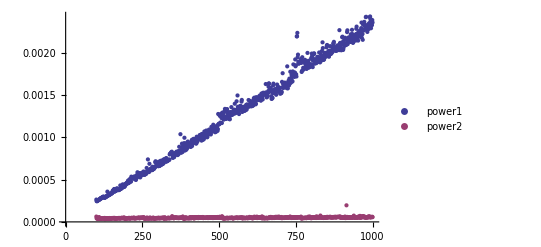

```mathematica
ListPlot[{times1,times2},PlotLegends->{"power1","power2"}]
```

This gives us a visual comparison of the time complexity of the two algorithms. You can see that the second approach significantly outperforms the first. It is left to the reader to compare the functions we created to Mathematica’s built-in PowerMod function.

### Recursion and Iteration

In this subsection we compare recursive and iterative approaches for computing factorial.

#### Recursive Factorial

First we will implement Algorithm 1 from Section 5.4, a recursive algorithm for computing n!. This function accepts a nonnegative integer n as its input. If the input value is 0, the function returns 1. Otherwise, it multiplies n by the value of the function applied to n-1.

```mathematica
factorialR[n_Integer]:=Module[{},
If[n==0,1,n*factorialR[n-1]]
]
```

Note that, while we could have defined the function’s action on n=0 and n≠0 without using the Module structure, a Module will be needed in the iterative version and in comparing performance of algorithms, it is important to keep as much of the implementations the same as possible.

We test this function on 10 and verify that it has the same result as Mathematica's built-in operator.

```mathematica
factorialR[10]
```

3628800

```mathematica
10!
```

3628800

#### Iterative Factorial

We can implement factorial with an iterative algorithm as well. Our function will use a variable f, initialized to 1, to store the value of the factorial. It will compute using a For loop with a loop variable running from 1 to n. Within the loop, f will be multiplied by the current value of the loop variable.

```mathematica
factorialI[n_Integer]:=Module[{f,i},
f=1;
For[i=1,i≤n,i++,
f=f*i
];
f
]
```

We again check to make sure the result is correct on n=10.

```mathematica
factorialI[10]
```

3628800

#### Comparing Recursion and Iteration

Note that these two algorithms require exactly the same number of multiplications. From this point of view, their complexity is the same.

However, let's look at their performance. We consider values of n from 1 to 1500. We use the same approach as we did for power1 and power2 above to record and plot the time performance.

```mathematica
timesR=Block[{$RecursionLimit=Infinity},Table[{n,Timing[factorialR[n]][[1]]},{n,1500}]];
```

```mathematica
timesI=Table[{n,Timing[factorialI[n]][[1]]},{n,1500}];
```

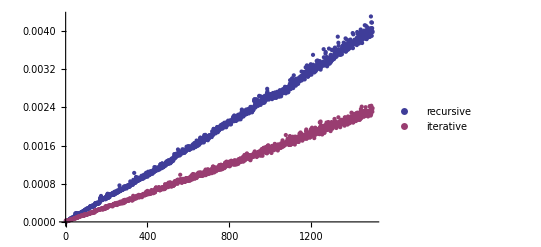

```mathematica
ListPlot[{timesR,timesI},PlotLegends->{"recursive","iterative"}]
```

First, you might wonder about the outliers which appear to be values of n for which one function or the other performs particularly poorly. These are essentially noise resulting from other processes on the computer. They are also inconsistent; running the commands again will produce slightly different results.

However, it is clear that, despite the occasional peculiar value, the iterative function outperforms the recursive one for large values of n. This is in spite of the fact that the two algorithms involve the same number of multiplications. Let's consider other sources of potential differences in complexity.

The For loop in the iterative function includes a comparison (i must be tested against n to determine if the loop continues) and the recursive function makes the comparison in the If statement. So the two functions are effectively equal in terms of the number of comparisons used.

The iterative function involves two assignments (the assignment of f and the implicit assignment of i when it is incremented) absent from the recursive version. But two assignments are much less costly than a function call. Recursive function calls require Mathematica to perform several operations in the background, both in order to execute the recursive call and to keep track of where Mathematica is in the chain of recursive calls. All of which takes time and memory that the iterative approach does not require.

It is important to keep in mind the cost of recursion. When an iterative algorithm is available, it may be more efficient. On the other hand, recursive algorithms are often more natural to use and can better reveal the mathematical concepts.

### Merge Sort

We conclude this section by implementing merge sort.

The merge sort algorithm is described in Algorithm 9 of the text. The mergeSort function will accept as its input a list of integers. Its main function is to split the single list it receives into two halves, unless the list contains only one element. The output of mergeSort is the result of applying mergeSort to both halves of the list and then recombining them with merge.

The following implements Algorithm 9. Note that the merge function will be written next. For now, Mathematica simply accepts merge as a symbol.

```mathematica
mergeSort[L:{__Integer}]:=Module[{m,L1,L2},
If[Length[L]>1,
m=Floor[Length[L]/2];
L1=L[[;;m]];
L2=L[[m+1;;]];
merge[mergeSort[L1],mergeSort[L2]],
(*else*)
L
]
]
```

Note the use of the Span (;;) operator to determine the two sublists. The syntax a;;b, within the Part ([[…]]) operator, is used to obtain the sublist of elements from position a to b. Omitting a, as in ;;5, obtains the elements from the beginning to position 5. And omitting b, as in 3;;, obtains the elements from position 3 to the end of the list.

#### Implementing Merge

To complete the function, we need to define merge. The merge function accepts two lists, which it assumes are sorted, and returns a single list that contains all the elements of both of the inputs and is sorted. The procedure is described in Algorithm 10 of the text.

In implementing merge, the first step is to duplicate the input lists. This is because the lists are emptied of their elements as the merge proceeds, and arguments to a function cannot be modified. We also initialize the list that will be the result to the empty list.

The main work of merge is contained in a While loop conditioned on both lists being nonempty. Within this While loop there are an If statement and a Which. The If statement will implement the instruction to “remove smaller of first elements of L_1 and L_2 from its list; put it at the right end of L” from Algorithm 10. This If statement will test whether the first element of L_1 is smaller than the first element of L_2. If so, then the first element is removed from L_1 and added to L. If not, in the else clause, the first element of L_2 is moved to L.

We use AppendTo to add elements to the end of the list L. Note that AppendTo, when applied to the name of a list and an element, automatically replaces the list stored in the symbol. We use Delete to remove the first element from the list. Delete is applied to a list and a position and returns the list with the element in that position removed. Unlike AppendTo, Delete does not automatically update a symbol representing a list, so we must reassign the name of the list to the result of the Delete.

The Which statement will implement the if statement found in Algorithm 10. The first condition will be that L_1 is empty, and if so the remainder of L_2 will be added to L and L_2 will be emptied. In a second condition, L_2 will be tested. Note that the Which is Mathematica’s answer to the else-if construction. Join is used to combine two lists.

Here is the implementation of merge.

```mathematica
merge[l1:{__Integer},l2:{__Integer}]:=Module[{L={},L1=l1,L2=l2},
While[(L1=!={})&&(L2=!={}),
If[L1[[1]]<L2[[1]],
AppendTo[L,L1[[1]]];
L1=Delete[L1,1],
(*else*)
AppendTo[L,L2[[1]]];
L2=Delete[L2,1]
];
Which[L1==={},
L=Join[L,L2];L2={},
L2==={},
L=Join[L,L1];L1={}
]
];
L
]
```

We apply mergeSort to a list as follows.

```mathematica
mergeSort[{7,4,1,5,2,3,6}]
```

{1,2,3,4,5,6,7}

#### Tracing Merge Sort

To better understand how functions work, it is sometimes useful to create “verbose” versions of them. That is, versions of the functions that use Print or other means to report on what it is that they are doing. We provide a verbose version of mergeSort and apply it to the list {3,1,2}.

```mathematica
mergeSortVerbose[L:{__Integer}]:=Module[{m,L1,L2},
Print["mergeSort called on ",L];
If[Length[L]>1,
m=Floor[Length[L]/2];
Print["m=",m];
L1=L[[;;m]];
Print["L1=",L1];
L2=L[[m+1;;]];
Print["L2=",L2];
merge[mergeSortVerbose[L1],mergeSortVerbose[L2]],
(*else*)
Print["length=1"];
L
]
]
```

```mathematica
mergeSortVerbose[{3,1,2}]
```

mergeSort called on {3,1,2}

m=1

L1={3}

L2={1,2}

mergeSort called on {3}

length=1

mergeSort called on {1,2}

m=1

L1={1}

L2={2}

mergeSort called on {1}

length=1

mergeSort called on {2}

length=1

{1,2,3}

We recommend reading through the output. Then try it with a larger example, say with 7 elements, to make sure that you understand how merge sort works. You can also create a verbose version of merge to see the details of how that function works.

## 5.5 Program Correctness

In this section we will prove the correctness of the merge sort program that we implemented in the last section. This will require that we prove the correctness of merge as well as mergeSort. We begin with merge.

### merge

For convenience, we will repeat the definition of merge. Also, we've added comments to indicate where we've broken the procedure into three segments: S_1, S_2, and S_3.

```mathematica
merge[l1:{__Integer},l2:{__Integer}]:=Module[{L,L1,L2},
(*begin S1*)
L={};
L1=l1;
L2=l2;
(*end S1*)
While[(L1=!={})&&(L2=!={}),
(*begin S2*)
If[L1[[1]]<L2[[1]],
AppendTo[L,L1[[1]]];
L1=Delete[L1,1],
(*else*)
AppendTo[L,L2[[1]]];
L2=Delete[L2,1]
];
(*end S2*)
(*begin S3*)
Which[L1==={},
L=Join[L,L2];L2={},
L2==={},
L=Join[L,L1];L1={}
]
(*end S3*)
];
L
]
```

Let p be the assertion that l_1 and l_2 (the inputs to the function) are ordered, nonempty, and disjoint lists of integers. Let q be the proposition that L (the output) is an ordered list and that L=l_1∪l_2 as sets (that is, the set of integers appearing in L is equal to the union of the set of integers appearing in l_1 and the set of integers in l_2). We claim that p{merge}q, i.e., that merge is partially correct with respect to the initial condition p and the final assertion q.

Let q_1 be the proposition that L_1=l_1, L_2=l_2, and L is the empty list. It is clear that p{S_1}p∧q_1.

Define the following propositional variables:

r_1 is the proposition that L_1 is a sublist of l_1; that is, the set of elements appearing in L_1 is a subset of the set of elements appearing in l_1, and the order of the elements in L_1 is the same as their order in l_1. Note that it immediately follows from p and r_1 that L_1 is ordered.

r_2 is the proposition that L_2 is a sublist of l_2 (and thus L_2 is ordered).

r_3 is the assertion that L is ordered.

r_4 is the assertion that L∪L_1∪L_2=l_1∪l_2 as sets.

r_5 is the proposition that all members of L are smaller than all members of L_1 and L_2. That is, (∀x∈L)(∀y∈L_1∪L_2)(x<y).

r is the proposition r_1∧r_2∧r_3∧r_4∧r_5.

We claim that p∧q_1→r. Assume p∧q_1. That is, l_1 and l_2 are ordered, nonempty, and disjoint lists of integers. Also, L_1=l_1, L_2=l_2, and L is empty. Then r_1 and r_2 hold since a list is a sublist of itself. Proposition r_3 holds since L is empty and thus is ordered vacuously. That r_4 is true follows from substituting l_1, l_2, and ∅ for L_1, L_2, and L. And r_5 is vacuous since L is empty. From p{S_1}p∧q_1 and (p∧q_1)→r, we have p{S_1}r.

Next, we will show that r is a loop invariant for the loop while (L_1≠{} and L_2≠{})S_2;S_3. Denote by c the condition L_1≠{}∧L_2≠{}. We must show that if r and c hold, then r is true after S_2;S_3 is executed. First we will show r∧c{S_2}r and then that r{S_3}r.

To show that r∧c{S_2}r, assume r∧c. That is, L_1 is a sublist of l_1, L_2 is a sublist of l_2, L is ordered, L∪L_1∪L_2=l_1∪l_2, and all members of L are smaller than every member of L_1 and L_2. Also, L_1 and L_2 are nonempty. Then both L_1 and L_2 have first elements. Assume that the if condition of S_2 holds. That is, the first element of L_1 is smaller than the first element of L_2. Then the two commands in the then clause of S_2 are executed: the first element of L_1 is added to the end of L and L_1 has its first element removed.

We need to show that r holds following the execution of the then clause of S_2.

r_1: the new L_1 is a sublist of the old L_1 since an element was removed meaning that L_(1new)⊂L_(1old) as sets and the order of the remaining elements was not modified. Since L_(1new) is a sublist of L_(1old) which was a sublist of l_1, the new L_1 is a sublist of l_1.

r_2: the new L_2 is identical is the old L_2 and thus remains a sublist of l_2.

r_3: the old L was ordered, and, since we assume that r_5 held before execution of S_2, every element of L_old was smaller than every element of L_(1old)∪L_(2old). In particular, the first element of L_(1old) was larger than all elements of L_old. And so L_new is ordered.

r_4: The smallest element of L_1 was removed from L_1 and added to L. Thus L_new∪L_(1new)=L_old∪L_(1old) and hence L∪L_1∪L_2=l_1∪l_2.

r_5: We must show that all members of L_new are smaller than all members of both L_(1new) and L_(2new). Let x be an arbitrary element of L_new. Either x was a member of L_old or x was the first element of L_(1old). If x was a member of L_old then the assumption that r_5 held before execution of S_2 guarantees that x is smaller than all elements of L_(1new)∪L_(2new). On the other hand, assume x was the first element of L_(1old). Since L_(1old) is a sublist of l_1, it is ordered and thus x was also the smallest element of L_(1old) and hence is less than all elements of L_(1new). Also, by the assumption that the if condition of S_2 evaluated true, x is smaller than the first (and smallest) element of L_(2old)=L_(2new) as well. So x is smaller than all members of L_(1new)∪L_(2new).

The above shows that if the if condition of S_2 holds, then r holds after executing the then clause. In case the condition fails and the else clause executes, the proof is similar. We conclude that r∧c{S_2}r.

Next we will show that r{S_3}r. Assume r holds. Consider the case that L_1 is empty. Then L_2 is appended onto the end of L and L_2 is set to the empty list.

r_1: L_1 is, since we assume the if condition, empty and thus a sublist of l_1.

r_2: the second statement in the then clause sets L_2 equal to the empty list, which is a sublist of l_2.

r_3: we assume that L_old is ordered, that L_(2old) is a sublist of l_2 and thus is ordered, and that all members of L_old are smaller than all members of L_(2old). Thus, adding L_(2old) to the end of L_old to produce L_new results in an ordered list.

r_4: as sets, L_new=L_old∪L_(2old), so L_new∪L_(1new)∪L_(2new)=(L_old∪L_(2old))∪L_(1old)∪∅. This is equal to l_1∪l_2 by the assumption that r_4 held before execution.

r_5: after execution of S_3, both L_1 and L_2 are empty and assertion r_5 is true vacuously.

The case that L_2 is empty is similar. Thus, r{S_3}r.

We have shown r∧c{S_2}r and r{S_3}r, and thus r∧c{S_2;S_3}r. Hence r is a loop invariant for the while loop. By the inference rule for while loops, we have that r{while c S_2;S_3}(¬c∧r).

Combining this result with the conclusion that p{S_1}r from the paragraph immediately following the definition of r, we have that p{merge}(¬c∧r).

We conclude by claiming ¬c∧r→q. Recall that q was the final assertion that L is ordered and L=l_1∪l_2 as sets. Assume ¬c∧r. That L is ordered is the claim of r_3. By r_4, we have that, as sets, L∪L_1∪L_2=l_1∪l_2. But ¬c implies that L_1 and L_2 are empty. Hence, L=l_1∪l_2. Thus q holds and we have completed the proof that p{merge}q and hence merge is partially correct.

### mergeSort

Now we turn to the mergeSort function. We repeat its definition below.

```mathematica
mergeSort[L:{__Integer}]:=Module[{m,L1,L2},
If[Length[L]>1,
m=Floor[Length[L]/2];
L1=L[[;;m]];
L2=L[[m+1;;]];
merge[mergeSort[L1],mergeSort[L2]],
(*else*)
L
]
]
```

Let p be the assertion that L is a nonempty list of distinct integers, and let q be the assertion that the function returns a list which has the same elements as L and is ordered. Our claim is that p{mergeSort}q. Since mergeSort is recursive, our proof will be by strong induction on the length of the list L.

For the basis case, assume that L has only one element. Also assume p. Then the if condition of mergeSort fails and the program terminates by returning L unmodified. But since L has only one element, it is trivially ordered. Thus, under the basis assumption that L has only one element, p{mergeSort}q.

For the inductive case, we make the inductive assumption that for all k≤n, if a list has length k then mergeSort returns the list sorted. Assume L has n+1 elements. Also assume p. Under these assumptions, the if condition is satisfied.

The first command in the then clause assigns m=⌊(n+1)/2⌋. Note that m<n+1 and, since n>1, m>0. All of the inequalities are strict.

The next two commands assign L_1 to the list consisting of the first m elements in L and L_2 to the remainder. Note that since 0<m<n+1, both of these lists are nonempty with at most n elements.

In the final statement of the if clause, mergeSort is applied to L_1 and to L_2. Since these two lists both have length at most n, the inductive assumption implies that the results of mergeSort on L_1 and L_2 are lists with the same elements and ordered. Since merge is partially correct, as shown in the previous subsection, the result of merge is an ordered list consisting of the elements of its input lists. Hence, the result of mergeSort is an ordered list consisting of the same elements as L. That is, q holds.

This concludes the inductive step and we conclude p{mergeSort}q for all lengths of L. Hence, mergeSort is partially correct.

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 2

Generate all well-formed formulae for expressions involving the variables x, y, and z and the operators ￼ {+,·,/,-} with n or fewer symbols.

Solution: This problem asks us to not only generate well-formed formulae, but to generate all such formulae subject to a limitation on the number of symbols.

To begin, we present a recursive definition of the set of well-formed formulae on the symbols.

Basis step: x, y, and z are well-formed formulae.

Recursive step: If F and G are well-formed formulae, then so are: (-F), (F+G), (F-G), (F·G), and (F/G).

Note that we will fully parenthesize the well-formed formulae so as to avoid ambiguity, but parentheses will not be considered symbols for the purpose of counting symbols in the formula.

Also note that we will implement the well-formed formulae as strings, not as algebraic expressions. The reason for this is that if we build algebraic expressions, Mathematica will perform unwanted simplification. For example, -(-x) is a well-formed formula distinct from x, but if we enter -(-x) as a Mathematica expression, it will be simplified to x.

We will approach this problem in two steps. First, we generate well-formed formulae using a function with sufficiently many applications of the recursive step to guarantee that every well-formed formula of length n or less is produced. Second, we will prune the well-formed formulae with greater than n symbols. This will leave us with all well-formed formulae involving at most n symbols.

#### Generating Formulae

The first step is to generate well-formed formulae. For this, we will create a pair of functions, similar to allStrings and buildStrings from Section 5.3 of this manual.

The function buildWFFs will accept a single argument, a list of well-formed formulae. It will apply the recursive step to the existing set. The function first makes a copy of the input set, since arguments cannot be modified. Second, using a Do loop over the input set, it applies unary negation. Then, with a Do loop over the input set and over the binary operations, the function adds the rest of the well-formed formulae.

```mathematica
buildWFFs[S_List]:=Module[{T=S,f,g,o},
Do[T=Union[T,{"(-"<>f<>")"}],{f,S}];
Do[T=Union[T,{"("<>f<>o<>g<>")"}],
{f,S},{g,S},{o,{"+","-","*","/"}}];
T
]
```

Let's confirm that this works as expected by applying it to the basis set {"x","y","z"}.

```mathematica
buildWFFs[{"x","y","z"}]
```

{(-x),x,(x*x),(x-x),(x+x),(x/x),(x*y),(x-y),(x+y),(x/y),(x*z),(x-z),(x+z),(x/z),(-y),y,(y*x),(y-x),(y+x),(y/x),(y*y),(y-y),(y+y),(y/y),(y*z),(y-z),(y+z),(y/z),(-z),z,(z*x),(z-x),(z+x),(z/x),(z*y),(z-y),(z+y),(z/y),(z*z),(z-z),(z+z),(z/z)}

Note that the order is not the order in which the well-formed formulae are added, it is the order that Union imposes on the set.

The other component is the function that calls buildWFFs. This is nearly identical to allStrings. allWFFs accepts a positive integer m representing the number of applications of the recursive step that are to be performed. It initializes the set of formulae to the basis set and applies buildWFFs as many times as is called for.

```mathematica
allWFFs[m_Integer]:=Module[{S,i},
S={"x","y","z"};
For[i=1,i≤m,i++,
S=buildWFFs[S]
];
S
]
```

Now the question is: how many applications of the recursive step are needed to be sure that the result contains all well-formed formulae of length at most n? Clearly, 0 applications of buildWFFs are needed to obtain all formulae consisting of 1 symbol, as this is the basis step. Also, the formulae produced by an application of buildWFFs contain at least one symbol more than was present in the previous step (from the unary negation). So after n-1 applications of buildWFFs, we are guaranteed to have all well-formed formulae with n symbols or fewer.

To illustrate, we will find all well-formed formulae of length at most 3. Apply AllWFFs to 2.

```mathematica
allWFF3=allWFFs[2];
```

We suppressed the output since the output would be lengthy.

```mathematica
Length[allWFF3]
```

7101

Here is the list of every 300th formula.

```mathematica
Table[allWFF3[[i]],{i,1,7101,300}]
```

{(-(-x)),((x-x)-(-y)),((x*x)*(z-x)),((x-y)+(x-x)),((x*y)-(y-y)),((x/y)*(z-y)),((x*z)+(x-z)),((x/z)-(y-z)),((-y)+(x+x)),(y-(x+y)),((y+x)*(z+x)),((y/y)+(x+x)),((y+y)-(y+y)),((y-y)*(z+z)),((y+z)+(x+z)),((y-z)+(-z)),((z+x)/x),((z-x)-(y/x)),((z*x)*(z/y)),((z-y)+(x/y)),((z*y)-(y/z)),((z/y)*(z/z)),((-z)+(z/y)),(z-(z/z))}

Note that these involve up to seven symbols. Since we want the formulae with at most three symbols, we must remove from this set all the formulae with more than three. For this, we will need a function that calculates the number of symbols in a formula.

#### Pruning the Set

To count the number of characters in a string, Mathematica provides the StringLength function. If you apply StringLength to a string, the command returns the number of characters in the string.

```mathematica
StringLength["abcde"]
```

5

However, the number of symbols in a well-formed formula is not equal to its length, since parentheses are not considered symbols. Fortunately, Mathematica also provides the function StringCount. This function takes two arguments. The first is the string. The second is a substring or a list of substrings that you wish to count within the first. For example, to determine the number of a’s and b’s within the string “abcccbabbcab”, you enter the following.

```mathematica
StringCount["abcccbabbcab",{"a","b"}]
```

8

To count the number of symbols in a well-formed formula, we apply StringCount with second argument the list of all symbols: {"x","y","z","+","-","*","/"}. For example, the number of symbols in "((z-x)-(z*x))" is:

```mathematica
StringCount["((z-x)-(z*x))",{"x","y","z","+","-","*","/"}]
```

7

In order to prune the set allWFF3 so that it contains only the formulae with 3 or fewer symbols, we’ll use the Select function. The Select function can be used to find the subset of a given set consisting of those elements satisfying a given condition. Select requires two arguments. The first is the original list. The second is a boolean-valued function of one argument that can be applied to the elements of the list and returns True for those elements that should be selected. The result is the list of elements of the original list for which the function returned true.

In our case, the Boolean-valued function should return true if the well-formed formula has three or fewer symbols. We will create a function to test the result of StringCount against 3.

```mathematica
testWFF3[s_String]:=StringCount[s,{"x","y","z","+","-","*","/"}]<=3
```

We can now use the name of this function as the second argument to Select.

```mathematica
Select[allWFF3,testWFF3]
```

{(-(-x)),(-x),x,(x*x),(x-x),(x+x),(x/x),(x*y),(x-y),(x+y),(x/y),(x*z),(x-z),(x+z),(x/z),(-(-y)),(-y),y,(y*x),(y-x),(y+x),(y/x),(y*y),(y-y),(y+y),(y/y),(y*z),(y-z),(y+z),(y/z),(-(-z)),(-z),z,(z*x),(z-x),(z+x),(z/x),(z*y),(z-y),(z+y),(z/y),(z*z),(z-z),(z+z),(z/z)}

It is left to the reader to generalize and combine these functions into a single function that accepts n as an argument and returns the list of all well-formed formulae with n or fewer symbols.

### Computations and Explorations 2

Determine which Fibonacci numbers are divisible by 5, which are divisible by 7, and which are divisible by 11. Prove that your conjectures are correct.

Solution: We use the Fibonacci function to determine the Fibonacci numbers. This function applied to an integer n returns the nth Fibonacci number.

To answer the first part of the question, we want to know which Fibonacci numbers are divisible by 5. That is, we want to determine for which n is the nth Fibonacci divisible by 5. We will construct a list consisting of those indices between 1 and 50 for which the corresponding Fibonacci number is divisible by 5.

```mathematica
Reap[For[n=1,n≤50,n++,
If[Divisible[Fibonacci[n],5],Sow[n]]
]]
```

{Null,{{5,10,15,20,25,30,35,40,45,50}}}

This list suggests that the nth Fibonacci number is divisible by 5 when n is. To obtain more evidence, we'll design a function to look for counterexamples to the assertion: F_n is divisible by 5 if and only if n is divisible by 5.

We first create a function that accepts a positive integer n and checks whether or not n is a counterexample of the assertion that F_n is divisible by 5 if and only if n is divisible by 5. If either F_n is not divisible by 5 when n is, or F_n is divisible by 5 when n is not, then this function will print a message to that effect.

```mathematica
checkFib5[n_Integer]:=Module[{F},
F=Fibonacci[n];
If[Divisible[F,5]&&Not[Divisible[n,5]],
Print["Fn="F," is not divisible by 5, but n=",n," is"]
];
If[Divisible[n,5]&&Not[Divisible[F,5]],
Print["Fn="F," is divisible by 5, but n=",n," is not"]
];
]
```

In order to check as many Fibonacci numbers as possible, while not spending too much time on the process, we will apply the TimeConstrained function. The first argument to TimeConstrained is an expression to be evaluated. In this case, the expression will be an infinite For loop that applies checkFib5. We make the loop infinite by entering True for the test. The second argument to TimeConstrained is the time, in seconds, that the expression should be allowed to run. TimeConstrained also accepts a third, optional, argument, that is evaluated if the first expression fails to finish. If the third argument is not given, the output in case the time runs out will be $Aborted. We will use a Print statement as the third argument to report the largest value of n for which F_n was checked. Note that we subtract one from the value of the loop variable since we cannot be certain whether the current value was in fact checked or if it was aborted.

Below, we allow the test to run for 3 seconds.

```mathematica
TimeConstrained[For[n=1,True,n++,checkFib5[n]],3,
Print["Checked through n=",n-1]]
```

Checked through n=58275

How many Fibonacci numbers can be checked will depend on your computer. Proving the conjecture, as well as forming and proving conjectures for 7 and 11, is left to the reader.

## Exercises

Use Mathematica to find and prove formulas for the sum of the first k nth powers of positive integers for n=4,5,6,7,8,9,10.

For what positive integers k is n^k-n divisible by k for all positive integers n?

Use Mathematica to help you find and prove the formulas sought in Exercises 9, 10, and 11 of Section 5.1 of the text. Do not use the symbolic capabilities of the Sum command to form your conjectures.

Find integers a and d such that d divides a^(n+1)+(a+1)^(2n-1) for all positive integers n. (Exercises 36 and 37 in Section 5.1 indicate that a=4,d=21 and a=11,d=133 are two such pairs.)

Supplementary Exercises 4 and 5 suggest a more general conjecture. Use Mathematica's Sum function to produce evidence for this conjecture.

Use the postageBasis algorithm from Section 5.2 of this manual to find the smallest n such that every amount of postage of n cents or more can be made from stamps worth 78 cents and $5.95.

Write a function that accepts two stamp denominations as input and returns the smallest n such that every amount of postage of n cents or more can be made from the given denominations, or returns $Failed if it cannot find such an n. Use your function to make a conjecture that describes for which pairs of denominations such an n exists and for which there is no such n.

Write a function to recursively build a set from the following definition: basis step: 2 and 3 belong to the set; recursive step: if x and y are members, then x·y is a member.

Use the Timing function to compare the performance of gR and gF from Section 5.3. Graph the time performance for the two functions. (Be sure to Clear gR prior to every execution so that the comparison is fair.)

Write a function that accepts two stamp denominations and returns all amounts of postage that can be paid with up to n stamps.

The solution provided for Computer Projects 2 is inefficient as a means of finding all well-formed formulae involving at most n symbols. This is because formulae which already have more symbols than the maximum are retained and used to produce even longer formulae. In particular, after n iterations, the resulting set includes formulae of up to 2^(n+1)-1 symbols (but not all such formulae). Modify the approach taken in the solution to Computer Projects 2 so that strings that include more than n symbols are pruned at each step of the recursion.

Write a function to compute the number of partitions of a positive integer (see Exercise 47 in Section 5.3 of the text).

Write a function to compute Ackermann's function (see the prelude to Exercise 48 in Section 5.3).

Implement Algorithm 3 for computing gcd(a,b) from Section 5.4 of the text.

Implement Algorithm 5, the recursive linear search algorithm, from Section 5.4 of the text.

Implement Algorithm 6, the recursive binary search algorithm, from Section 5.4 of the text.

Compare the performance of your implementations of Algorithm 5 and Algorithm 6 as follows: for a variety of values of n, let L be the list of integers from 1 to n. Randomly choose one hundred integers between 1 and n and measure the average of the times taken for each algorithm to find the randomly chosen integers. Graph n versus the average times. (RandomInteger[{min,max},count] will output a list of count randomly chosen integers between min and max.)

Create three functions to compute Fibonacci numbers: an iterative function, a recursive function that stores values, and a recursive function that does not store values. Base your functions on Algorithms 7 and 8 in Section 5.4 of the text. Create a graph illustrating the time performance of the three functions.

Implement quick sort, described in the prelude to Exercise 50 in Section 5.4 of the text. Compare the performance with the merge sort implemented in this manual.

Implement the algorithm described in Supplementary Exercise 44 for expressing a rational number as a sum of Egyptian fractions.

Use Mathematica to study the McCarthy 91 function. (See the prelude to problem 45 in the Supplementary Exercises of Chapter 5.)